# Лабораторная работа 2.4 Компьютерная сцинтилляционная γ - спектроскопия

## Введение

Цель работы: определить зависимость энергии и интенсивности гамма-линий от различных гамма источников и идентифицировать их.

В работе используются : сцинтиллятор, ФЭУ, предусилитель импульсов, высоковольтный блок питания для ФЭУ, АЦП, компьютер.

### Теоретическое введение

#### Фотоэффект

Это процесс взаимодействия гамма - кванта с электроном, связанным с атомом, при котором электрону передается вся энергия гамма - кванта.При этом электрону сообщается кинетическая энергия T_e=E_γ-I_i, где E_γ– энергия гамма - кванта, I_i– потенциал ионизации i - той оболочки атома.Фотоэффект особенно существенен для тяжелых веществ, где он идет с заметной вероятностью даже при высоких энергиях гамма - квантов.В легких веществах фотоэффект становится заметен лишь при относительно небольших энергиях гамма - квантов.Наряду с фотоэффектом, при котором вся энергия гамма - кванта передается атомному электрону, взаимодействие гамма - излучения со средой может приводить к его рассеянию, т.е.отклонению от первоначального направления распространения на некоторый угол.

#### Эффект Комптона.

Это упругое рассеяние фотона на свободном электроне, сопровождающееся изменением длины волны фотона (реально этот процесс происходит на слабо связанных с атомом внешних электронах).Максимальная энергия образующихся комптоновских электронов соответствует рассеянию гамма - квантов на 180° и равна

E_max==(η ω)/(1+(m c^2)/(2η ω))

#### Процесс образования электрон - позитронных пар.

При достаточно высокой энергии гамма - кванта наряду с фотоэффектом и эффектом Комптона может происходить третий вид взаимодействия гамма - квантов с веществом-- образование электрон - позитронных пар.Процесс образования пар не может происходить в пустоте, так как в этом случае не выполняются законы сохранения энергии и импульса.В присутствии ядра или электрона процесс образования пары гамма - квантов возможен, так как можно распределить энергию и импульс гамма - кванта между тремя частицами без противоречия с законами сохранения.При этом если процесс образования пары идет в кулоновском поле ядра или протона, то энергия образующегося ядра отдачи оказывается весьма малой, так что пороговая энергия гамма - кванта E_0, необходимая для образования пары, практически совпадает с удвоенной энергией покоя электрона E_0=2m c^2 = 1.022 МэВ.
Появивишийся в результате процесса образования пар электрон свою энергию на ионизацию среды. Таким образом, вся энергия электрона остается в детекторе. Позитрон будет двигаться до тех пор, пока практически не остановится, а затем аннигилирует с электроном среды, в результате чего появятся два гамма-кванта. Т.е., кинетическая энергия позитрона также останется в детекторе. Далее возможны три варианта развития событий:

оба родившихся гамма-кванта не вылетают из детектора, и тогда вся энергия первичного гамма-кванта останется в детекторе, а в спектре появится пик с

один из родившихся гамма-квантов покидает детектор, и в спектре появляется пик, соответствующий энергии

оба родившихся гамма-кванта покидают детектор, и в спектре появляется пик, соотвествующий энергии

```mathematica
Calibration=Import["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Phys_Labs/5_sem/Lab555/Нехаев 08-11-2018/calibration.xlsx"][[1]][[7;;All]];
```

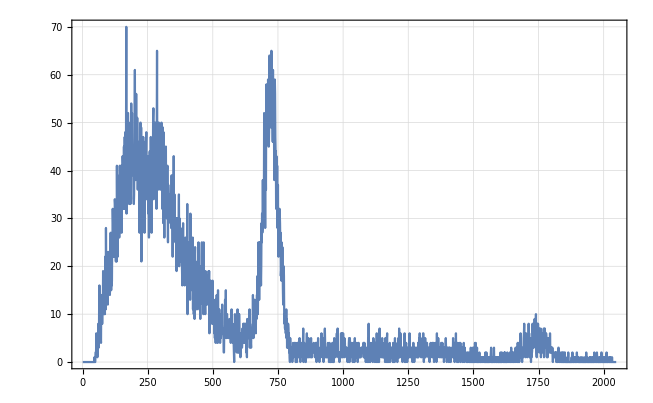

```mathematica
ListLinePlot[Calibration, PlotTheme->"Detailed"]
```

```mathematica
Show[%15,FrameLabel->{{HoldForm[Counts],None},{HoldForm[N],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

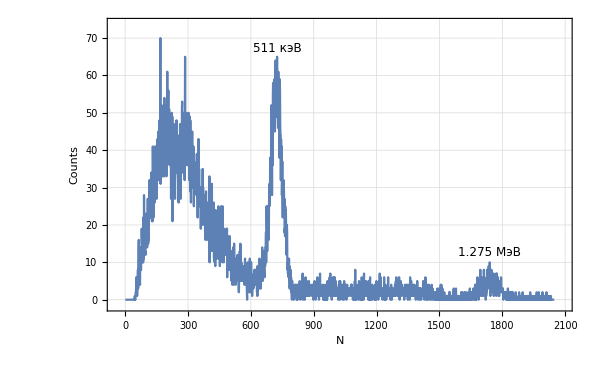

```mathematica
GaussianFit[leftBorder_,rightBorder_,data_]:=
FindFit[data,{a*Exp[-(x-x0)^2/(2*sigma^2)]+b*x+c,{leftBorder≤ x0≤ rightBorder}},{a, x0, sigma, b, c},x];
```

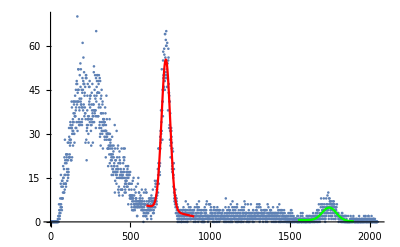

```mathematica
leftBorder = 600;
rightBorder = 900;
leftBorder2 = 1550;
rightBorder2 = 1900;
Peak511Calibration=Calibration[[leftBorder;;rightBorder]];
Peak1275Calibration=Calibration[[leftBorder2;;rightBorder2]];
GaussianModel[x_]=a*Exp[-(x-x0)^2/(2*sigma^2)]+b*x+c;
fit=FindFit[Peak511Calibration,{GaussianModel[x],{leftBorder≤ x0≤ rightBorder}},{a, x0, sigma, b, c},x];
fit2=FindFit[Peak1275Calibration,{GaussianModel[x],{leftBorder2≤ x0≤ rightBorder2}},{a, x0, sigma, b, c},x];
Show[ListPlot[Calibration],Plot[GaussianModel[x]/.fit,{x,leftBorder,rightBorder},PlotStyle->Red],Plot[GaussianModel[x]/.fit2,{x,leftBorder2,rightBorder2},PlotStyle->Green]]
```

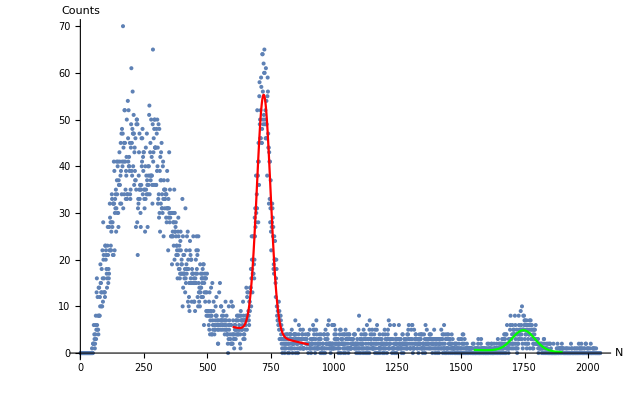

```mathematica
Show[%398,AxesLabel->{HoldForm[N],HoldForm[Counts]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotTheme->"Detailed"]
```

```mathematica
fit
```

{a→51.2362,x0→722.438,sigma→-26.9278,b→-0.012576,c→13.1519}

```mathematica
fit2
```

{a→4.47316,x0→1746.,sigma→44.2973,b→-0.00132674,c→2.72292}

```mathematica
Calibrator=({{511*1000, 722.438}, {1275*1000, 1745.9955}});
LinearModelFit[Calibrator,x,x]
```

FittedModel[37.8334+0.00133973 x]

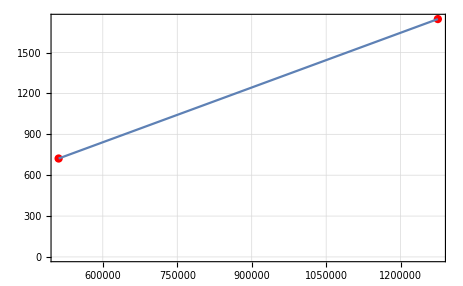

```mathematica
Show[ListPlot[Calibrator,PlotStyle->Red,PlotTheme->"Detailed"],Plot[%410[x],{x,511000,1275000}]]
```

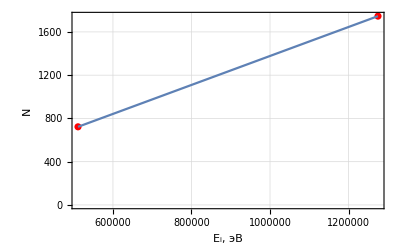

```mathematica
Show[%413,FrameLabel->{{HoldForm[N],None},{RawBoxes[RowBox[{SubscriptBox["E","i"],","," ","эВ"}]],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Normal[%410]
```

37.8334+0.00133973 x

```mathematica
Reduce[y== 37.83344175392632+0.001339734947643979 x,x]
```

x==-28239.5+746.416 y

```mathematica
Calibrate[y_]:=-28239.497536777086+746.4162980584872 y;
```

```mathematica
Calibrate[722.438]
```

511000.